## Calculating Phase Matching Conditions; Everything starts with the Sellmeier Equations. This is for the collinear regime. Assuming monochromatic pump, uniaxial crystals and an infinitely large crystal.

Sellmeier Equations for BBO

```mathematica
<<"ErrorBarPlots`"
Off[General::"spell1"]
Off[General::"spell"]
Off[General::"pspec"]
ordindex[λ_]:=√(2.7359+0.01878/(λ λ-0.01822)-0.01354 λ λ);
extindex[λ_]:=√(2.3753+0.01224/(λ λ-0.01667)-0.01516 λ λ);
airindex[λ_]:=1.000287566+1.3412/((10^18 (λ λ))/10^12);
```

Refractive indices for pump and degenerate wavelength in BBO

```mathematica
BB=ordindex[0.405]^2
CC=extindex[0.405]^2 
AA=ordindex[0.81]^2
DD=extindex[0.81]^2
```

2.86248

2.45588

2.75646

2.3845

Angle of Optical Axis to Pump Wave Vector for Degenerate Collinear Phase Matching

```mathematica
Θ=ArcCos[Sqrt[(CC/AA -1)*(BB/(CC-BB))]]*180/π
```

28.8159

Calculating non-degenerate uses a slightly more complicated equation

```mathematica
λp=0.405;
λs=0.76;λi=λs*λp/(λs-λp)
nop=ordindex[λp];nep=extindex[λp];nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];nairi=airindex[λi];nairs=airindex[λs];
Θ=ArcCos[Sqrt[(λs^2*λi^2/(λp^2*(λi*nos +λs*noi)^2) -1/nep^2)*(nop^2*nep^2)/(nep^2-nop^2)]]*180/π
```

0.867042

28.7591

## Lateral Walkoff Calculation for Pump

```mathematica
15.76Tan[ArcTan[(BB/CC) Tan[Θ]]-Θ]
5.35Tan[ArcTan[(BB/CC) Tan[Θ]]-Θ]
```

1.03855

0.352553

## Lateral Walkoff Calculation for SPDC

```mathematica
15.76Tan[ArcTan[(nos/nes)^2Tan[Θ]]-Θ]
```

0.982314

Calculating the angles needed to get a particular wavelength to be collinear. We also plot the results.

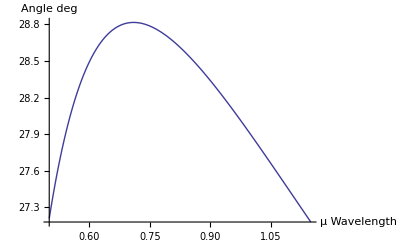

```mathematica
thetafinder[incre_]:=Module[{theta,λp,λs,λi,nop,nep,nos,nes,noi,nei},λp=0.405;λs=0.6+incre 0.0005;λi=(λs λp)/(λs-λp);nop=ordindex[λp];nep=extindex[λp];nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];theta=(ArcCos[√((((λs^2 λi^2)/(λp^2 (λi nos+λs noi)^2)-1/nep^2) (nop^2 nep^2))/(nep^2-nop^2))] 180)/π;Return[theta];]
WAVELENGTHLIMIT=1300;
Clear[thetalist,index];
thetalist=Table[0,{i,WAVELENGTHLIMIT}];
For[index=1,index<WAVELENGTHLIMIT+1,thetalist⟦index⟧=thetafinder[index];index++;];
DataTable=Table[{0.5+i 0.0005,thetalist⟦i⟧},{i,WAVELENGTHLIMIT}];
ListPlot[DataTable,AxesLabel->{Wavelength μ,Angle deg},Joined->True]
```

here we calculate the phase function against exit angle, fixing other quantities

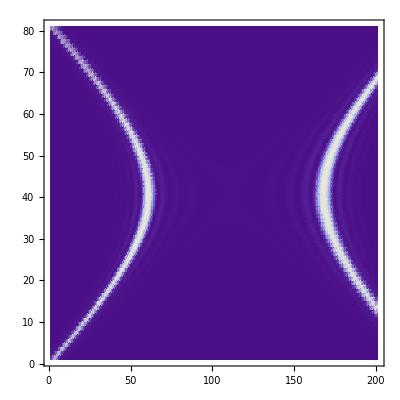

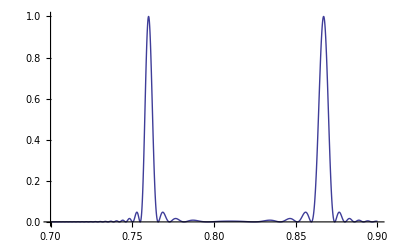

```mathematica
phasefunction[thetas_,λs_]:=Module[
{Φ,λp,λi,c,nop,nep,nos,nes,noi,nei,npeff,ωp,ωs,ωi,Θp,Θs,Θi,L,W,δkz,δky,δkx},
λp=0.405;λi=λs*λp/(λs-λp);
nop=ordindex[λp];nep=extindex[λp];
nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];nairi=airindex[λi];nairs=airindex[λs];
Θp=28.7591π/180;
Θs=ArcSin[Sin[thetas*π/180]*nairs/nos];(*emissionangle inside the crystal*)
Θi=ArcSin[nos*ωs*Sin[Θs]/(noi*ωi)];
ωp=2*π/λp;ωs=2*π/λs;ωi=2*π/λi;
       npeff=Sqrt[1/((Cos[Θp]/nop)^2 + (Sin[Θp]/nep)^2)];
L=15760; (*length of crystal*)
W=82;(*waist of pump *)
δkz=(npeff*ωp -nos*ωs*Cos[Θs] - noi*ωi*Cos[Θi]);
δkx=0;
δky=(-nos*ωs*Sin[Θs] + noi*ωi*Sin[Θi]);
Φ=Exp[-W^2(δkx^2 + δky^2)/2]*(Sin[δkz*L/2]/(δkz*L/2))^2;
Return[Φ];
];
ListDensityPlot[Table[phasefunction[x,y],{x,-2,2,0.05},{y,0.7,0.9,0.001}],Mesh->False,PlotRange->{0,1}]
Plot[phasefunction[0,x],{x,0.7,0.9},PlotRange->Full]
```

now we integrate over a range of angles

```mathematica
ThetaResolution=0.01;
ThetaEvents = 2*ThetaLimit/ThetaResolution +1;
AcceptanceAngleIntegrate[λs_]:=Module[{θs},
(*Run the trapezoid rule*)
IntegratedPhaseValue=0;
For[θs=-ThetaLimit,θs<ThetaLimit,θs+=ThetaResolution,IntegratedPhaseValue+=ThetaResolution*(phasefunction[θs,λs]+phasefunction[θs+ThetaResolution,λs])/2.0];
Return[IntegratedPhaseValue];
];
(*
ThetaLimit=1.2;
(*Generate list for ThetaLimit=1.2*)
ThetaLimit12=Table[AcceptanceAngleIntegrate[λ],{λ,0.7,0.9,0.001}];
Print["1.2 done"];

ThetaLimit=1.1;
(*Generate list for ThetaLimit=1.1*)
ThetaLimit11=Table[AcceptanceAngleIntegrate[λ],{λ,0.7,0.9,0.001}];
Print["1.1 done"];

ThetaLimit=1.0;
(*Generate list for ThetaLimit=1.0*)
ThetaLimit10=Table[AcceptanceAngleIntegrate[λ],{λ,0.7,0.9,0.001}];
Print["1.0 done"];

ThetaLimit=0.9;
(*Generate list for ThetaLimit=0.9*)
ThetaLimit09=Table[AcceptanceAngleIntegrate[λ],{λ,0.7,0.9,0.001}];
Print["0.9 done"];

ThetaLimit=0.8;
(*Generate list for ThetaLimit=0.8*)
ThetaLimit08=Table[AcceptanceAngleIntegrate[λ],{λ,0.7,0.9,0.001}];
Print["0.8 done"];

ThetaLimit=0.7;
(*Generate list for ThetaLimit=0.7*)
ThetaLimit07=Table[AcceptanceAngleIntegrate[λ],{λ,0.7,0.9,0.001}];
Print["0.7 done"];

ThetaLimit=0.6;
(*Generate list for ThetaLimit=0.6*)
ThetaLimit06=Table[AcceptanceAngleIntegrate[λ],{λ,0.7,0.9,0.001}];
Print["0.6 done"];

ThetaLimit=0.5;
(*Generate list for ThetaLimit=0.5*)
ThetaLimit05=Table[AcceptanceAngleIntegrate[λ],{λ,0.7,0.9,0.001}];
Print["0.5 done"];

ThetaLimit=0.4;
(*Generate list for ThetaLimit=0.4*)
ThetaLimit04=Table[AcceptanceAngleIntegrate[λ],{λ,0.7,0.9,0.001}];
Print["0.4 done"];

ThetaLimit=0.3;
(*Generate list for ThetaLimit=0.3*)
ThetaLimit03=Table[AcceptanceAngleIntegrate[λ],{λ,0.7,0.9,0.001}];
Print["0.3 done"];

ThetaLimit=0.2;
(*Generate list for ThetaLimit=0.2*)
ThetaLimit02=Table[AcceptanceAngleIntegrate[λ],{λ,0.7,0.9,0.001}];
Print["0.2 done"];
*)

ThetaLimit=0.13;
(*Generate list for ThetaLimit=0.1*)
ThetaLimit013thin=Table[AcceptanceAngleIntegrate[λ],{λ,0.7,0.9,0.001}];
Print["0.13 done"];

ThetaLimit=0.1;
(*Generate list for ThetaLimit=0.1*)
ThetaLimit01=Table[AcceptanceAngleIntegrate[λ],{λ,0.7,0.9,0.001}];
Print["0.1 done"];

(*Generate list for collinear direction*)
ThetaLimit00=Table[phasefunction[0,λ],{λ,0.7,0.9,0.001}];
Print["Collinear direction done"];
```

0.13 done

0.1 done

Collinear direction done

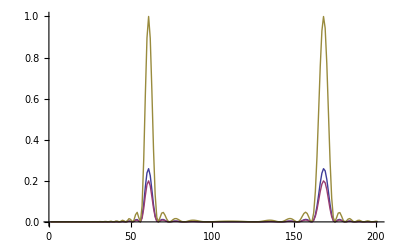

```mathematica
ListPlot[{ThetaLimit013thin,ThetaLimit01,ThetaLimit00},Joined->True,PlotRange->Full]
```

```mathematica
(*SetDirectory["/photonics/staff/Alex/data/021015"];*)
(*Export["ThetaLimit12.dat",ThetaLimit12];
Export["ThetaLimit11.dat",ThetaLimit11];
Export["ThetaLimit10.dat",ThetaLimit10];
Export["ThetaLimit09.dat",ThetaLimit09];
Export["ThetaLimit08.dat",ThetaLimit08];
Export["ThetaLimit07.dat",ThetaLimit07];
Export["ThetaLimit06.dat",ThetaLimit06];
Export["ThetaLimit05.dat",ThetaLimit05];
Export["ThetaLimit04.dat",ThetaLimit04];
Export["ThetaLimit03.dat",ThetaLimit03];*)
Export["ThetaLimit013thin.dat",ThetaLimit013thin];
Export["ThetaLimit01.dat",ThetaLimit01];
Export["ThetaLimit00.dat",ThetaLimit00];
```